Rupture behavior in a 1D regularized, variational, fracture model

The governing nonlinear of the system 

φ_(,ξξ)-α^2φ +(β^2 α^2)/(1-φ)^3=0

We are going to derive the stress–strain response of the 1D bar using the shooting method. These results are going to complement the results obtained by Kaushik using FEA. The goal is to c

```mathematica
(*Initialization. This cell  initialises the important variables.*)


ClearAll["Global`*"]
c=N[√27/256]
ShootingPoints={0.0,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,0.999,0.9999};
```

```mathematica
(*Initialization. This cell  initialises the important variables.*)
f[βs_,αs_]:=Module[{α=αs,β=βs,sols},sols=Map[First[NDSolve[{ϕ''[ξ]-α^2 ϕ[ξ]+(β^2 α^2)/(1-ϕ[ξ])^3==0,ϕ'[0]==0,ϕ'[1]==0},ϕ,ξ, Method->"BoundaryValues"->{"Shooting", "StartingInitialConditions"->{ϕ[0] == #, ϕ'[0] == 0}},MaxSteps->1000000]]&,
ShootingPoints];
sols
(*Plot[Evaluate[ϕ[ξ] /. sols], {ξ,0,1}, PlotStyle->{Black, Blue, Green,Brown, Purple, Gray, Red, Magenta, Yellow}]*)
]
Plotϕ[ks_,solss_]:=Module[{k=ks,sols=solss},
Plot[Evaluate[ϕ[ξ]/.sols[[k,1]]],{ξ,0,1}]]

ComputeStrain[ks_,solss_,βs_]:=Module[{k=ks,sols=solss,dummy,β=βs},
dummy[ξ_]:=Evaluate[ϕ[ξ]/.sols[[k,1]]];
β*NIntegrate[1/(1-dummy[ξ])^2,{ξ,0,1}]
]
```

```mathematica
(*Initialization*)
Clear[solnum,α,βVec,ϵVec];

α=√10;
βVec=Range[0,1,0.05]*c;
N1=Length[βVec];
N2=Length[ShootingPoints];
solnum=Range[1,N2];
ϵVec=Table[0,{i,1,N1},{j,1,N2}];
```

{0.,0.016238,0.032476,0.0487139,0.0649519,0.0811899,0.0974279,0.113666,0.129904,0.146142,0.16238,0.178618,0.194856,0.211094,0.227332,0.24357,0.259808,0.276046,0.292284,0.308522,0.32476}

```mathematica
For[i=0,i< N1,i++;
Clear[βi,solsi,strainsi];
βi=βVec[[i]];
Print[βi];
solsi=f[βi,α];
p1=Plotϕ[2,solsi];
strainsi=Map[ComputeStrain[#,solsi,βi]&,solnum];
ϵVec[[i,;;]]=strainsi;
]
```

0.

0.016238

0.032476

0.0487139

0.0649519

0.0811899

0.0974279

0.113666

0.129904

0.146142

0.16238

0.178618

0.194856

0.211094

0.227332

0.24357

0.259808

0.276046

0.292284

0.308522

0.32476

ReplaceAll::reps: 0.263671875`/(1 - ϕ[« 1 »])^3 - 10 ϕ[ξ] + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand 1 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

ReplaceAll::reps: 0.263671875`/(1 - ϕ[« 1 »])^3 - 10 ϕ[ξ] + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand 1 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

ReplaceAll::reps: 0.263671875`/(1 - ϕ[« 1 »])^3 - 10 ϕ[ξ] + SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand 1 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

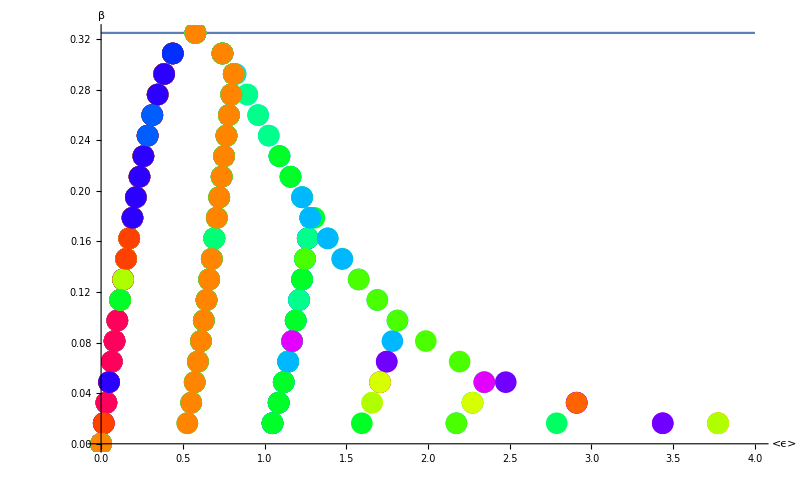

```mathematica
Clear[pold,pnew, data];
pold=Plot[c,{x,0,4}];
For[i=0,i< N2,i++;
Clear[data];
data=Reverse[Transpose[{βVec[[;;]],ϵVec[[;;,i]]}],2];
pnew=ListPlot[data,PlotStyle->Hue[Random[]]];
pold=Show[pold,pnew,PlotRange->All,AxesLabel->{
Style["<ϵ> ",Black,FontFamily->"TimesNewRoman",30],
Style["β",Black,FontFamily->"TimesNewRoman",30]},
ImageSize->800,
GridLines->None,
AxesStyle->Directive[Black,Thickness[0.001],FontFamily->"Times New Roman",18]
];
]

pold
```

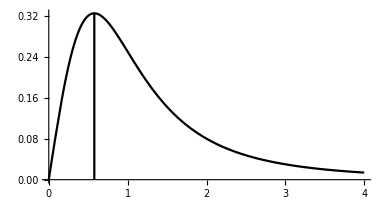

```mathematica
p5=ParametricPlot[{{ϵ̃,(ϵ̃)/((1+(ϵ̃)^2)^2)},{1/(√3),(ϵ̃)/4 c}},{ϵ̃,0,4},PlotStyle->{Black}]
```

```mathematica
pold
```

pold

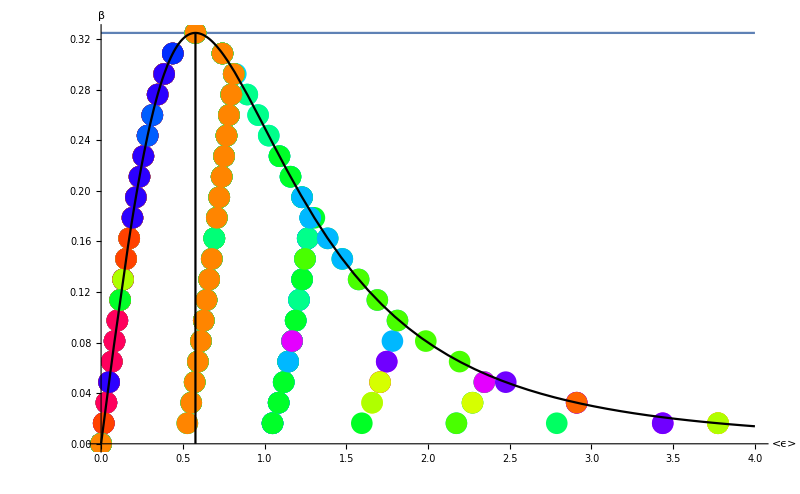

```mathematica
Show[pold,p5]
```

Figure: Non-unique stress-strain response. The figure shows the non-dimensional force, β, as a function of the average, relative strain  ⟨ϵ̃⟩. The colored circles mark the (β, ⟨ϵ̃⟩) points that correspond to the numerically computed, plausible,  damaged states of the bar. The hortizontal and the vertical dashed lines mark the critical stress and strain β_c and (ϵ̃)_c, respectively. The solid black line is the stress-strain reponse, eq (),  when it is assumed that the plausible damaged state is always homogenous. 
-Graphics-